```mathematica
(1/Sqrt[2])-1
```

```mathematica
FullSimplify[-1+1/(√2)]
```

-1+1/(√2)

```mathematica
p[j_]:=((kt)^j/j!)Exp[-kt]
```

```mathematica
Sum[2j p[2j],{j,0,Infinity}]
```

ⅇ^-kt kt Sinh[kt]

```mathematica
Plot[Sinh[kt],{kt,0,100}]
```

-Graphics-

```mathematica
ⅇ^-kt kt (kt Cosh[kt]+Sinh[kt])-(ⅇ^-kt kt Sinh[kt])^2
```

-ⅇ^(-2 kt) kt^2 Sinh[kt]^2+ⅇ^-kt kt (kt Cosh[kt]+Sinh[kt])

```mathematica
Simplify[-ⅇ^(-2 kt) kt^2 Sinh[kt]^2+ⅇ^-kt kt (kt Cosh[kt]+Sinh[kt])]
```

ⅇ^(-2 kt) kt (ⅇ^kt kt Cosh[kt]+Sinh[kt] (ⅇ^kt-kt Sinh[kt]))

```mathematica
f[kt_]:=(ⅇ^(-2 kt) kt (ⅇ^kt kt Cosh[kt]+Sinh[kt] (ⅇ^kt-kt Sinh[kt])))/(ⅇ^-kt kt Sinh[kt])
```

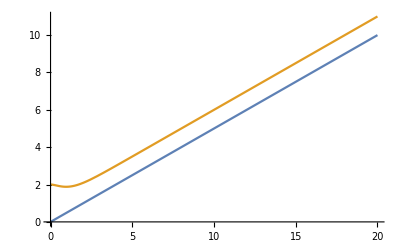

```mathematica
Plot[{0.5 kt,f[kt]},{kt,0,20}]
```

```mathematica
f[10]/10
```

(10 ⅇ^10 Cosh[10]+(ⅇ^10-10 Sinh[10]) Sinh[10])/ⅇ^20

```mathematica
N[(10 ⅇ^10 Cosh[10]+(ⅇ^10-10 Sinh[10]) Sinh[10])/ⅇ^20]
```

3.

```mathematica
N[(10 (10 ⅇ^10 Cosh[10]+(ⅇ^10-10 Sinh[10]) Sinh[10]))/ⅇ^20]
```

30.

```mathematica
f[20]/20
```

(20 ⅇ^20 Cosh[20]+(ⅇ^20-20 Sinh[20]) Sinh[20])/ⅇ^40

```mathematica
N[(20 ⅇ^20 Cosh[20]+(ⅇ^20-20 Sinh[20]) Sinh[20])/ⅇ^40]
```

5.5

```mathematica
N[(20 (20 ⅇ^20 Cosh[20]+(ⅇ^20-20 Sinh[20]) Sinh[20]))/ⅇ^40]
```

110.

```mathematica
p[j_]:=((k t)^j/j!)e^(-k t)/(e^(-k t) Cosh[k t])
```

```mathematica
Sum[n p[2n],{n,0,Infinity}]
```

1/2 k t Tanh[k t]

```mathematica
Sum[(n)^2p[2n],{n,0,Infinity}]
```

1/4 k t (k t+Tanh[k t])

(k t)/4

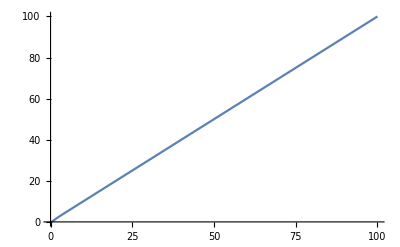

```mathematica
FullSimplify[1/4 k t (k t+1) - (1/2 k t )^2]

Plot[x Tanh[x],{x,0,100}]
```

```mathematica
Simplify[-1/4 k^2 t^2 Tanh[k t]^2+1/4 k t (k t+Tanh[k t])]
```

1/4 k t (k t Sech[k t]^2+Tanh[k t])

```mathematica
(1/4 k t (k t+1)-(1/2 k t 1)^2)/(1/2 k t )
```

(2 (-1/4 k^2 t^2+1/4 k t (1+k t)))/(k t)

```mathematica
Simplify[(2 (-1/4 k^2 t^2+1/4 k t (1+k t)))/(k t)]
```

1/2

```mathematica
Simplify[(2 (-1/4 k^2 t^2+1/4 k t (1+k t)))/k]
```

t/2

```mathematica
Simplify[(2 Coth[k t] (-1/4 k^2 t^2 +1/4 k t (k t+1)))/(k t)]
```

1/2 Coth[k t]

```mathematica
Manipulate[Plot[1/2+k t Csch[2 k t],{t,-0.9384433418879201,10}],{k,-0.9384433418879201,1.5615566581120799}]
```